```mathematica
list1=Transpose[{Table[i,{i,-10,10}],{356,411,476,543,622,704,793,860,923,967,982,967,923,859,786,700,618,545,467,405,349}}];(*圆线圈*)
list2=Transpose[{Table[i,{i,-10,10}],{879,985,1089,1186,1270,1334,1372,1396,1405,1409,1408,1408,1406,1394,1369,1332,1261,1178,1078,973,858}}];(*亥姆霍兹线圈,d=R,轴向*)
list3=Transpose[{Table[i,{i,-10,10}],{736,851,980,1119,1267,1415,1556,1675,1760,1813,1828,1805,1740,1650,1530,1387,1246,1106,972,846,729}}];(*亥姆霍兹线圈,d=1/2 R,轴向*)
list4=Transpose[{Table[i,{i,-5,5}],{1522,1439,1387,1355,1338,1332,1334,1351,1382,1429,1508}}];(*亥姆霍兹线圈,d=R,径向*)
list5=Transpose[{Table[i,{i,-10,10}],{1069,1073,1049,1010,950,894,834,782,744,720,711,718,736,771,822,879,937,996,1042,1072,1076}}];(*亥姆霍兹线圈,d=2R,轴向*)
```

```mathematica
R=0.1;i=0.4;u0=4Pi*10^-7;n=400;
B1=Table[{100x,1*10^6*(u0*n*i*R^2)/(2*(R^2+x^2)^(3/2))},{x,-0.1,0.1,0.01}];
B2=Table[{100x,1*10^6*(u0*n*i*R^2)/(2*(R^2+(x-0.05)^2)^(3/2))+1*10^6*(u0*n*i*R^2)/(2*(R^2+(x+0.05)^2)^(3/2))},{x,-0.1,0.1,0.01}];
B3=Table[{100x,1*10^6*(u0*n*i*R^2)/(2*(R^2+(x-0.025)^2)^(3/2))+1*10^6*(u0*n*i*R^2)/(2*(R^2+(x+0.025)^2)^(3/2))},{x,-0.1,0.1,0.01}];
B4=Transpose[{Table[i,{i,-5,5}],Table[Integrate[1*10^6*(n*u0*i*R)/(4*Pi)*((R-a*Cos[x])/((a^2+R^2-2*a*R*Cos[x])^(3/2))+(R-a*Cos[x])/((a^2+2 R^2-2*a*R*Cos[x])^(3/2))),{x,0,2Pi}],{a,-0.05,0.05,0.01}]}];
B5=Table[{100x,1*10^6*(u0*n*i*R^2)/(2*(R^2+(x-0.1)^2)^(3/2))+1*10^6*(u0*n*i*R^2)/(2*(R^2+(x+0.1)^2)^(3/2))},{x,-0.1,0.1,0.01}];
```

```mathematica
TableForm[Transpose[{First/@list1,Last/@list1,SetAccuracy[Last/@B1,1],SetPrecision[Abs[#[[2]][[2]]-#[[1]][[2]]]/(#[[2]][[2]])&/@Transpose[{list1,B1}]*100,3]}],TableHeadings->{None,{"轴向距离x/cm","B_(:5b9e:9a8c)/µT","µ_0/(2 SuperscriptBox[(SuperscriptBox[R, 2] + SuperscriptBox[x, 2]), FractionBox[3, 2]])/µT","相对误差/%"}},TableAlignments->Center]
TableForm[Transpose[{First/@list2,Last/@list2,SetAccuracy[Last/@B2,1],SetPrecision[Abs[#[[2]][[2]]-#[[1]][[2]]]/(#[[2]][[2]])&/@Transpose[{list2,B2}]*100,4]}],TableHeadings->{None,{"轴向距离x/cm","B_(:5b9e:9a8c)/µT","µ_0/(2*SuperscriptBox[(SuperscriptBox[R, 2] + SuperscriptBox[(x - R), 2]), FractionBox[3, 2]])+µ_0/(2*SuperscriptBox[(SuperscriptBox[R, 2] + SuperscriptBox[(x + R), 2]), FractionBox[3, 2]])/µT","相对误差/%"}},TableAlignments->Center]
TableForm[Transpose[{First/@list3,Last/@list3,SetAccuracy[Last/@B3,1],SetPrecision[Abs[#[[2]][[2]]-#[[1]][[2]]]/(#[[2]][[2]])&/@Transpose[{list3,B3}]*100,4]}],TableHeadings->{None,{"轴向距离x/cm","B_(:5b9e:9a8c)/µT","µ_0/(2*SuperscriptBox[(SuperscriptBox[R, 2] + SuperscriptBox[(x - FractionBox[R, 4]), 2]), FractionBox[3, 2]])+µ_0/(2*SuperscriptBox[(SuperscriptBox[R, 2] + SuperscriptBox[(x + FractionBox[R, 4]), 2]), FractionBox[3, 2]])/µT","相对误差/%"}},TableAlignments->Center]
TableForm[Transpose[{First/@list4,Last/@list4,SetPrecision[Last/@B4,4],SetPrecision[Abs[#[[2]][[2]]-#[[1]][[2]]]/(#[[2]][[2]])&/@Transpose[{list4,B4}]*100,4]}],TableHeadings->{None,{"径向距离x/cm","B_(:5b9e:9a8c)/µT",Style["∫_0^(2  π) µ_0/(4 π)((R - x*Cos[ß])/(SuperscriptBox[x, 2] + SuperscriptBox[R, 2] - 2*x*R*Cos[ß])^(3/2)+(R - x*Cos[ß])/(SuperscriptBox[x, 2] + 2 SuperscriptBox[R, 2] - 2*x*R*Cos[ß])^(3/2))ⅆß/µT",10],"相对误差/%"}},TableAlignments->Center]
TableForm[Transpose[{First/@list5,Last/@list5,SetAccuracy[Last/@B5,1],SetPrecision[Abs[#[[2]][[2]]-#[[1]][[2]]]/(#[[2]][[2]])&/@Transpose[{list5,B5}]*100,3]}],TableHeadings->{None,{"轴向距离x/cm","B_(:5b9e:9a8c)/µT","µ_0/(2*SuperscriptBox[(SuperscriptBox[R, 2] + SuperscriptBox[(x - R), 2]), FractionBox[3, 2]])+µ_0/(2*SuperscriptBox[(SuperscriptBox[R, 2] + SuperscriptBox[(x + R), 2]), FractionBox[3, 2]])/µT","相对误差/%"}},TableAlignments->Center]
TableForm[{{"飞行模式时","3 µT"},{"2格4G信号","3 µT"},{"WLAN开启","3 µT"},{"Bluetooth开启","3 µT"}},TableHeadings->{None,{"状态","磁场大小"}}]
```

轴向距离x/cm | B_实验/µT | µ_0/(2 SuperscriptBox[(SuperscriptBox[R, 2] + SuperscriptBox[x, 2]), FractionBox[3, 2]])/µT | 相对误差/%
-10 | 356 | 355. | 0.16
-9 | 411 | 413. | 0.446
-8 | 476 | 479. | 0.557
-7 | 543 | 553. | 1.76
-6 | 622 | 634. | 1.87
-5 | 704 | 719. | 2.13
-4 | 793 | 805. | 1.45
-3 | 860 | 883. | 2.65
-2 | 923 | 948. | 2.62
-1 | 967 | 990. | 2.36
0 | 982 | 1005. | 2.32
1 | 967 | 990. | 2.36
2 | 923 | 948. | 2.62
3 | 859 | 883. | 2.76
4 | 786 | 805. | 2.32
5 | 700 | 719. | 2.69
6 | 618 | 634. | 2.5
7 | 545 | 553. | 1.4
8 | 467 | 479. | 2.44
9 | 405 | 413. | 1.9
10 | 349 | 355. | 1.81

轴向距离x/cm | B_实验/µT | µ_0/(2*SuperscriptBox[(SuperscriptBox[R, 2] + SuperscriptBox[(x - R), 2]), FractionBox[3, 2]])+µ_0/(2*SuperscriptBox[(SuperscriptBox[R, 2] + SuperscriptBox[(x + R), 2]), FractionBox[3, 2]])/µT | 相对误差/%
-10 | 879 | 891. | 1.338
-9 | 985 | 1002. | 1.703
-8 | 1089 | 1111. | 2.004
-7 | 1186 | 1212. | 2.116
-6 | 1270 | 1296. | 2.037
-5 | 1334 | 1361. | 1.965
-4 | 1372 | 1403. | 2.227
-3 | 1396 | 1427. | 2.141
-2 | 1405 | 1436. | 2.169
-1 | 1409 | 1439. | 2.052
0 | 1408 | 1439. | 2.133
1 | 1408 | 1439. | 2.121
2 | 1406 | 1436. | 2.099
3 | 1394 | 1427. | 2.281
4 | 1369 | 1403. | 2.441
5 | 1332 | 1361. | 2.112
6 | 1261 | 1296. | 2.731
7 | 1178 | 1212. | 2.776
8 | 1078 | 1111. | 2.994
9 | 973 | 1002. | 2.901
10 | 858 | 891. | 3.696

轴向距离x/cm | B_实验/µT | µ_0/(2*SuperscriptBox[(SuperscriptBox[R, 2] + SuperscriptBox[(x - FractionBox[R, 4]), 2]), FractionBox[3, 2]])+µ_0/(2*SuperscriptBox[(SuperscriptBox[R, 2] + SuperscriptBox[(x + FractionBox[R, 4]), 2]), FractionBox[3, 2]])/µT | 相对误差/%
-10 | 736 | 760. | 3.132
-9 | 851 | 877. | 2.918
-8 | 980 | 1006. | 2.589
-7 | 1119 | 1145. | 2.312
-6 | 1267 | 1290. | 1.784
-5 | 1415 | 1433. | 1.231
-4 | 1556 | 1565. | 0.5659
-3 | 1675 | 1678. | 0.1694
-2 | 1760 | 1764. | 0.223
-1 | 1813 | 1818. | 0.2547
0 | 1828 | 1836. | 0.4274
1 | 1805 | 1818. | 0.6948
2 | 1740 | 1764. | 1.357
3 | 1650 | 1678. | 1.659
4 | 1530 | 1565. | 2.227
5 | 1387 | 1433. | 3.186
6 | 1246 | 1290. | 3.412
7 | 1106 | 1145. | 3.447
8 | 972 | 1006. | 3.384
9 | 846 | 877. | 3.488
10 | 729 | 760. | 4.053

径向距离x/cm | B_实验/µT | ∫_0^(2  π) µ_0/(4 π)((R - x*Cos[ß])/(SuperscriptBox[x, 2] + SuperscriptBox[R, 2] - 2*x*R*Cos[ß])^(3/2)+(R - x*Cos[ß])/(SuperscriptBox[x, 2] + 2 SuperscriptBox[R, 2] - 2*x*R*Cos[ß])^(3/2))ⅆß/µT | 相对误差/%
-5 | 1522 | 1556. | 2.154
-4 | 1439 | 1470. | 2.097
-3 | 1387 | 1417. | 2.085
-2 | 1355 | 1384. | 2.096
-1 | 1338 | 1366. | 2.075
0 | 1332 | 1361. | 2.112
1 | 1334 | 1366. | 2.367
2 | 1351 | 1384. | 2.385
3 | 1382 | 1417. | 2.438
4 | 1429 | 1470. | 2.777
5 | 1508 | 1556. | 3.054

轴向距离x/cm | B_实验/µT | µ_0/(2*SuperscriptBox[(SuperscriptBox[R, 2] + SuperscriptBox[(x - R), 2]), FractionBox[3, 2]])+µ_0/(2*SuperscriptBox[(SuperscriptBox[R, 2] + SuperscriptBox[(x + R), 2]), FractionBox[3, 2]])/µT | 相对误差/%
-10 | 1069 | 1095. | 2.39
-9 | 1073 | 1092. | 1.74
-8 | 1049 | 1063. | 1.32
-7 | 1010 | 1014. | 0.437
-6 | 950 | 954. | 0.453
-5 | 894 | 891. | 0.345
-4 | 834 | 831. | 0.329
-3 | 782 | 781. | 0.179
-2 | 744 | 742. | 0.211
-1 | 720 | 719. | 0.162
0 | 711 | 711. | 0.0195
1 | 718 | 719. | 0.116
2 | 736 | 742. | 0.866
3 | 771 | 781. | 1.23
4 | 822 | 831. | 1.11
5 | 879 | 891. | 1.34
6 | 937 | 954. | 1.82
7 | 996 | 1014. | 1.82
8 | 1042 | 1063. | 1.98
9 | 1072 | 1092. | 1.83
10 | 1076 | 1095. | 1.76

状态 | 磁场大小
飞行模式时 | 3 µT
2格4G信号 | 3 µT
WLAN开启 | 3 µT
Bluetooth开启 | 3 µT

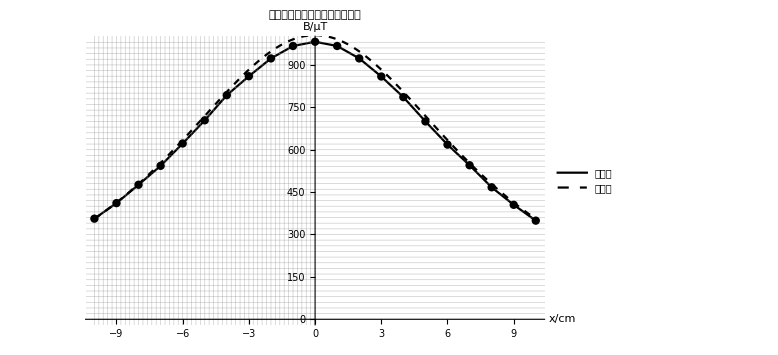

```mathematica
Show[ListPlot[list1,Joined->True,GridLines->{Join[Table[i,{i,-10,10,0.2}],Table[{i,Thick},{i,-10,10,1}]],Join[Table[i,{i,0,2000,20}],Table[{i,Thick},{i,0,2000,100}]]},ImageSize->Large,Mesh->All,PlotStyle->Black,PlotLegends->{"实验值"}],Plot[1*10^6*(u0*n*i*R^2)/(2*(R^2+(x/100)^2)^(3/2)),{x,-10,10},PlotStyle->{Black,Dashed},PlotLegends->{"理论值"}],AxesLabel->{"x/cm","B/µT"},PlotLabel->Style["载流圆单线圈轴线上磁场分布图",18,Black]]
```

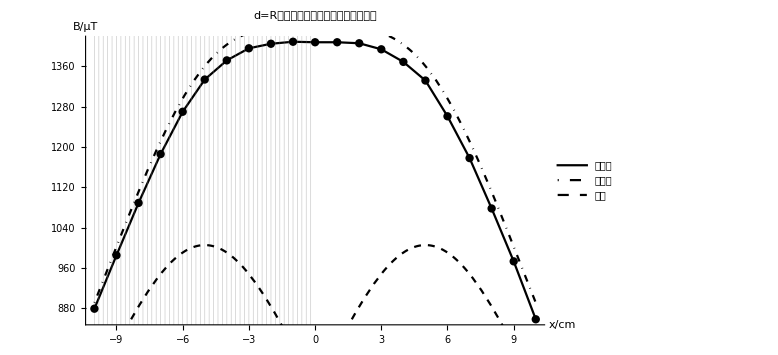

```mathematica
Show[ListPlot[list2,Joined->True,GridLines->{Join[Table[i,{i,-10,10,0.2}],Table[{i,Thick},{i,-10,10,1}]],Join[Table[i,{i,0,2000,10}],Table[{i,Thick},{i,0,2000,50}]]},ImageSize->Large,AspectRatio->0.618,Mesh->All,PlotStyle->Black,PlotLegends->{"实验值"}],Plot[1*10^6*(u0*n*i*R^2)/(2*(R^2+((x-5)/100)^2)^(3/2))+1*10^6*(u0*n*i*R^2)/(2*(R^2+((x+5)/100)^2)^(3/2)),{x,-10,10},PlotStyle->{Black,DotDashed,Thick},PlotLegends->{"理论值"}],
Plot[{1*10^6*(u0*n*i*R^2)/(2*(R^2+((x-5)/100)^2)^(3/2)),1*10^6*(u0*n*i*R^2)/(2*(R^2+((x+5)/100)^2)^(3/2))},{x,-10,10},PlotStyle->{{Black,Dashed}},PlotLegends->{"分部"}],AxesLabel->{"x/cm","B/µT"},PlotLabel->Style["d=R时亥姆霍兹线圈轴线上磁场分布图",18,Black]]
```

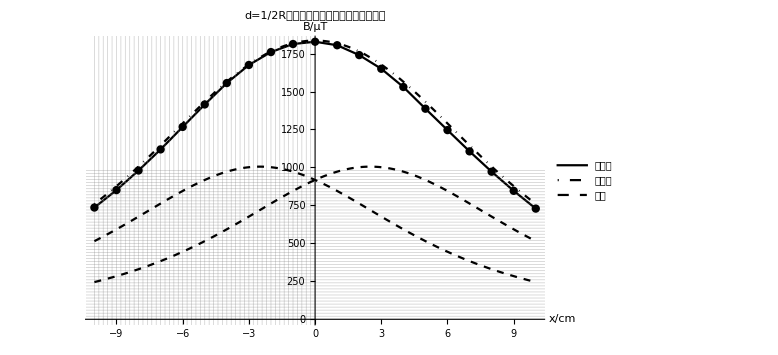

```mathematica
Show[ListPlot[list3,Joined->True,GridLines->{Join[Table[i,{i,-10,10,0.2}],Table[{i,Thick},{i,-10,10,1}]],Join[Table[i,{i,0,2000,20}],Table[{i,Thick},{i,0,2000,100}]]},ImageSize->Large,Mesh->All,PlotStyle->Black,PlotLegends->{"实验值"}],Plot[1*10^6*(u0*n*i*R^2)/(2*(R^2+((x-2.5)/100)^2)^(3/2))+1*10^6*(u0*n*i*R^2)/(2*(R^2+((x+2.5)/100)^2)^(3/2)),{x,-10,10},PlotStyle->{Black,DotDashed,Thick},PlotLegends->{"理论值"}],
Plot[{1*10^6*(u0*n*i*R^2)/(2*(R^2+((x-2.5)/100)^2)^(3/2)),1*10^6*(u0*n*i*R^2)/(2*(R^2+((x+2.5)/100)^2)^(3/2))},{x,-10,10},PlotStyle->{{Black,Dashed}},PlotLegends->{"分部"}],AxesLabel->{"x/cm","B/µT"},PlotLabel->Style["d=1/2R时亥姆霍兹线圈轴线上磁场分布图",18,Black]]
```

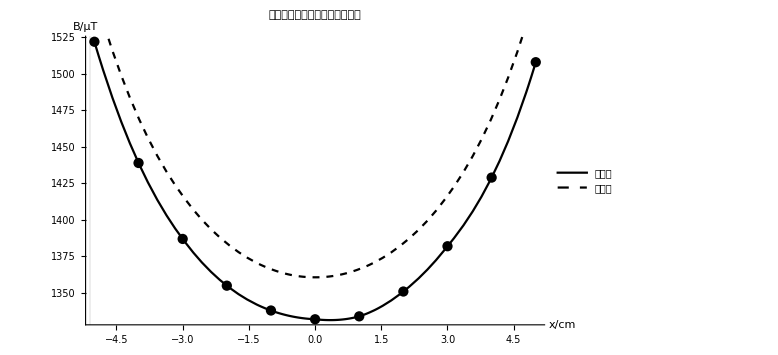

```mathematica
Show[ListPlot[list4,GridLines->{Join[Table[i,{i,-10,10,0.1}],Table[{i,Thick},{i,-10,10,0.5}]],Join[Table[i,{i,0,2000,2.5}],Table[{i,Thick},{i,0,2000,25}]]},ImageSize->Large,PlotStyle->Black],
Plot[Interpolation[list4][x],{x,-5,5},PlotStyle->Black,PlotLegends->{"实验值"}],Plot[Interpolation[B4][x],{x,-5,5},PlotStyle->{Dashed,Black},PlotLegends->{"理论值"}],AxesLabel->{"x/cm","B/µT"},PlotLabel->Style["载流圆单线圈轴线上磁场分布图",18,Black]]
```

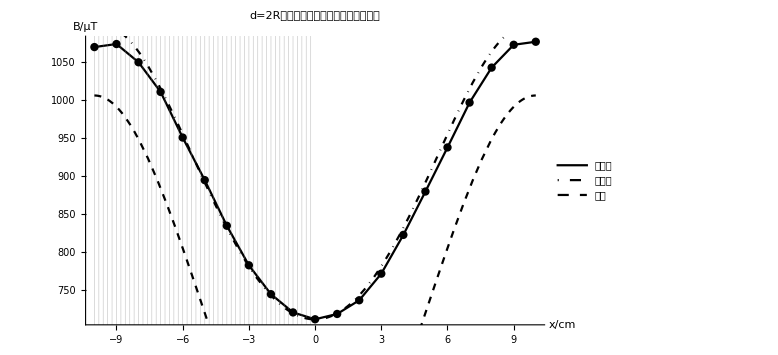

```mathematica
Show[ListPlot[list5,Joined->True,GridLines->{Join[Table[i,{i,-10,10,0.2}],Table[{i,Thick},{i,-10,10,1}]],Join[Table[i,{i,0,2000,5}],Table[{i,Thick},{i,0,2000,50}]]},ImageSize->Large,Mesh->All,PlotStyle->Black,PlotLegends->{"实验值"}],Plot[1*10^6*(u0*n*i*R^2)/(2*(R^2+((x-10)/100)^2)^(3/2))+1*10^6*(u0*n*i*R^2)/(2*(R^2+((x+10)/100)^2)^(3/2)),{x,-10,10},PlotStyle->{Black,DotDashed,Thick},PlotLegends->{"理论值"}],
Plot[{1*10^6*(u0*n*i*R^2)/(2*(R^2+((x-10)/100)^2)^(3/2)),1*10^6*(u0*n*i*R^2)/(2*(R^2+((x+10)/100)^2)^(3/2))},{x,-10,10},PlotStyle->{{Black,Dashed}},PlotLegends->{"分部"}],AxesLabel->{"x/cm","B/µT"},PlotLabel->Style["d=2R时亥姆霍兹线圈轴线上磁场分布图",18,Black]]
```